```mathematica
"tempRhoSimplePlot";
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
```

```mathematica
SetDirectory@NotebookDirectory[];
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Basic setup"]
```

Basic setup

```mathematica
<<MaTeX`
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm}"}(*,"Magnification"->1.2*)];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["MaTeX Loaded"]
```

MaTeX Loaded

```mathematica
(*<<ErrorBarPlots`*)
```

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x);
HideText["omarker & colors"]
```

omarker & colors

```mathematica
tempRhoRaw=Import["data.xlsx"]⟦1⟧⟦3;;24,{6,14}⟧;
HideText["tempRhoRaw; temp in Celsius, rho in Ohm.cm"]
```

tempRhoRaw; temp in Celsius, rho in Ohm.cm

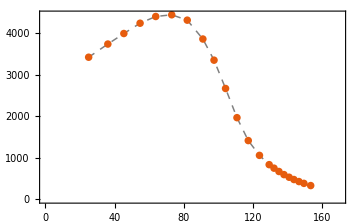

tempRhoPlot.pdf

```mathematica
tempRhoPlot=Show[ListLinePlot[tempRhoRaw,
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->{Dashed,Thickness[.003],Gray},
PlotRange->{{0,170},Automatic},
PlotRangePadding->{{0,0},{0,500}},
ImagePadding->{{45,45},{25,30}},
ImageSize->Medium,
GridLines->None],
ListPlot[tempRhoRaw,
PlotStyle->{PointSize[.015],colors⟦1⟧}],
Epilog->(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"T / \\si{\\celsius}",Scaled[{1.085,0}]},
{"\\rho / \\pqty{\\si{\\ohm\\cdot\\cm}}",Scaled[{0,1.08}]}
},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@tempRhoPlot
AutoCollapse[];
```

```mathematica
tempHallRaw=Import["data.xlsx"]⟦1⟧⟦3;;24,{6,23}⟧;
HideText["tempHallRaw; temp in Celsius, hall in 10^4.cm^3.C"]
```

tempHallRaw; temp in Celsius, hall in 10^4.cm^3.C

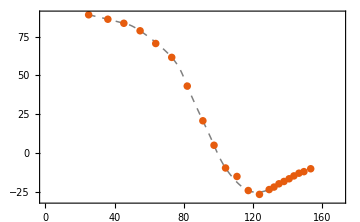

tempHallPlot.pdf

```mathematica
tempHallPlot=Show[
ListLinePlot[
Evaluate@Select[
!MemberQ[tempHallRaw⟦{5,11,13}⟧,#]&]@tempHallRaw,
InterpolationOrder->3,
PlotTheme->"Scientific",
(*PlotMarkers->{omarker,.012},*)
PlotStyle->{Dashed,Thickness[.003],Gray},
PlotRange->{{0,170},{-30,Automatic}},
PlotRangePadding->{{0,0},{10,15}},
ImagePadding->{{45,45},{25,30}},
ImageSize->Medium,
Axes->{True,False},
AxesStyle->Directive[Gray,Dotted],
GridLines->None],
ListPlot[tempHallRaw,
PlotStyle->{PointSize[.015],colors⟦1⟧}],
Epilog->(Inset[Evaluate@MaTeX[#1,
Magnification->.9],#2]&)@@@{
{"T / \\si{\\celsius}",Scaled[{1.085,0}]},
{"R_H / \\pqty{\\SI{e4}{\\cm^3.\\coulomb}}",Scaled[{0,1.08}]}
},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@tempHallPlot
AutoCollapse[];
```